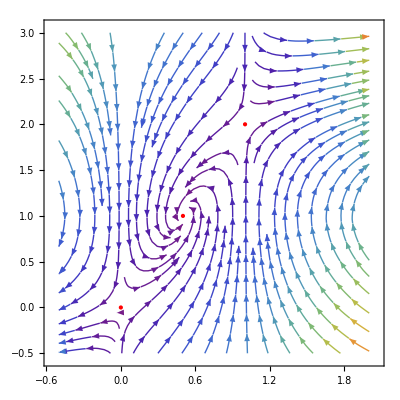

```mathematica
splot=StreamPlot[{{x*(1-x)*(1-y),x-0.5*y}},{x,-0.5,2},{y,-0.5,3},StreamColorFunction->"Rainbow",Epilog->{Red,PointSize[Medium],Point[{0,0}], Red,PointSize[Medium],Point[{1,2}],Red,PointSize[Medium],Point[{0.5,1}]}]
```

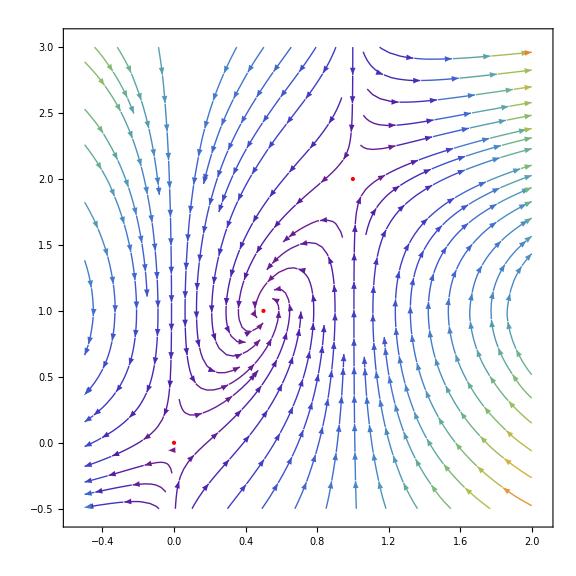

```mathematica
ss=Show[splot,ImageSize->Large]
```

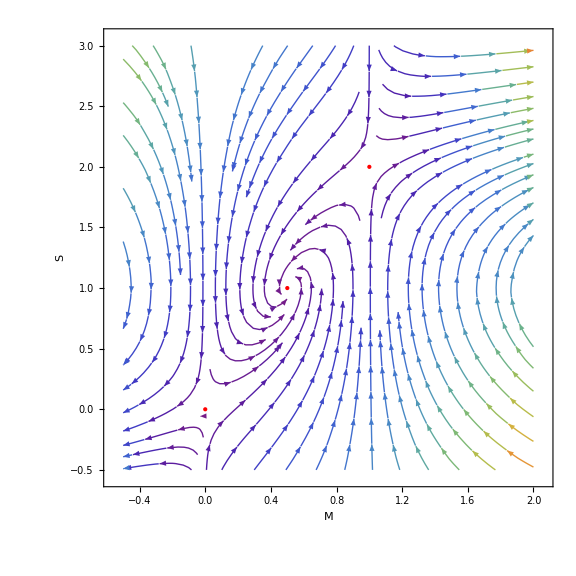

```mathematica
ss2=Show[ss,FrameLabel->{{HoldForm[S],None},{HoldForm[M],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",14,GrayLevel[0]}]
```

```mathematica
Export[NotebookDirectory[]<>"MS_Phase_plot.eps",ss2,"EPS"]
```